#### Import data

```mathematica
(* import the data sheet *)
all=Import[NotebookDirectory[]<>"LOUPE_Graph-based_AllSamples.csv"];
L=Length[all];
Print["Cells in the entire data set:"]
L-1
(* 
this data is 2 time L,
the number of lines, L-1, is equal to the total number of cells kept by LOUPE browser (where samples are calle "Library ID") after cellranger_aggr normalized the data,
the data does not contain genes any more,
the 1. column contains information about the BARCODE and the sample in which that barcode was found followed by -x, where x is the sample ID, e.g. GATTACCA-x, x=1,2,3,4,5,6, 
*)
(* 
this loop extracts the   
*)
sub={}&/@Range[1,6,1];
AppendTo[
sub⟦
ToExpression[StringTake[all⟦#,1⟧,-1]]
⟧
,all⟦#⟧
]&/@Range[2,L,1];
Print["Cells in each sample (027pre, 035pre, 027post, 035post, h1, h2):"]
sizes=Length[sub⟦#⟧]&/@Range[1,sub//Length,1]

(* this is literally a checksum *)
Print["Checksum:"]
Total[sizes]
(* 
this function f[];
takes a fixed numner of clusters (23), and an element of the data table sub⟦⟧;
calculates the number of cells within sub⟦⟧ that are found to be in each cluster;
returns a 3D data field with total number of cells per cluster for that sample (1st), and the fraction of cells (2nd, normalized to tootal cell count in the sample),
and the total number of cells again, as a control (3rd);
here, "sample" can also be replaced by a bundle of samples
*)

f[a_]:=Module[
{p1,l1,p2,l2,clusterCount,q1,q2,AD,CVM,KS,WUS,WSR},
l1=Length[a];
clusterCount=23;
p1=0&/@Range[1,clusterCount,1];
Table[
If[a⟦l,2⟧=="Cluster "<>ToString[#],p1⟦#⟧++]&/@Range[1,clusterCount,1];
,{l,1,l1}];
{p1,p1/Total[p1]//N,Total[p1]}
](* END of MODULE *)
```

Cells in the entire data set:

13878

Cells in each sample (027pre, 035pre, 027post, 035post, h1, h2):

{3831,1904,3340,750,1811,2242}

Checksum:

13878

#### Conditions per cluster: Majority Color Code, Export “colorListHEX.csv”

```mathematica
(*
Here, "condition" referes to healthy, pre BMT, or post BMT. We ask for the relative contribution of each condition in each cluster

sample IDs and cell counts are:
1 : AML027-pre, 3831 cells
2 : AML035-pre, 1904 cells
3 : AML027-post, 3340 cells
4 : AML035-post, 750 cells
5 : helathy1, 1811 cells
6 : helathy2, 2242 cells
*)
pre=f[Join[sub⟦1⟧,sub⟦2⟧]]⟦1⟧;
post=f[Join[sub⟦3⟧,sub⟦4⟧]]⟦1⟧;
healthy=f[Join[sub⟦5⟧,sub⟦6⟧]]⟦1⟧;
L=Total[{Total[pre],Total[post],Total[healthy]}];
c=pre//Length;

(* this function could plot a pie chart for each cluster, presenting the relaive abundances of each condition within that cluster *)
pc[k_]:=PieChart[{pre⟦k⟧,post⟦k⟧,healthy⟦k⟧}
,SectorOrigin->{Automatic,1}
,ChartStyle->{
Opacity[0.7,Darker[Red]]
,Opacity[0.7,Darker[Green]]
,Gray
}
];

(* this function assigns a single color based on the majority condition *)
majority[k_]:=Module[(* k is the cluster/subpopulation ID *)
{},
list={pre⟦#⟧,post⟦#⟧,healthy⟦#⟧}&/@Range[1,c,1];(* list of conditions *) 
m=Max[list⟦k⟧]; (* find which condition is the majority *)
p=Position[list⟦k⟧,m]⟦1,1⟧;(* return the index ("integer position=1,2,3") of the max *)
Which[
p==1,"#FF7575",(* Red for AML cases pre BMT *)
p==2,"#C16FD6",(* Purple for AML cases post BMT *)
p==3,"#BABABA" (* Gray for healthy *)
](* assign a color in HEX color code depending on the majority condition in that cluster k *)
]
(* Export the list of colors, to be used by dendro.R *)
colorList=majority[#]&/@Range[1,c,1];
Export[NotebookDirectory[]<>"colorListHEX.csv",{colorList},"CSV"];
```

#### Stacked Bar Chart of Fractions per Cluster

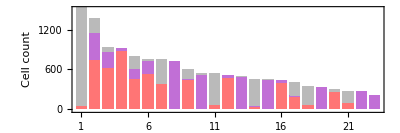

```mathematica
(*
Here, "condition" referes to healthy, pre BMT, or post BMT. We ask for the relative contribution of each condition in each cluster

sample IDs and cell counts are:
1 : AML027-pre, 3831 cells
2 : AML035-pre, 1904 cells
3 : AML027-post, 3340 cells
4 : AML035-post, 750 cells
5 : helathy1, 1811 cells
6 : helathy2, 2242 cells
*)
pre=f[Join[sub⟦1⟧,sub⟦2⟧]]⟦1⟧;
post=f[Join[sub⟦3⟧,sub⟦4⟧]]⟦1⟧;
healthy=f[Join[sub⟦5⟧,sub⟦6⟧]]⟦1⟧;
L=Total[{Total[pre],Total[post],Total[healthy]}];
c=pre//Length;
list={pre⟦#⟧,post⟦#⟧,healthy⟦#⟧}&/@Range[1,c,1];(* list of conditions *) 
hexToRGB=RGBColor@@(IntegerDigits[#~StringDrop~1~FromDigits~16,256,3]/255.)&;

bc=BarChart[
list
,ChartLayout->(*"Percentile"*)"Stacked"
,ChartStyle->{hexToRGB["#FF7575"],hexToRGB["#C16FD6"],hexToRGB["#BABABA"]}
,Frame->True(*{{False,False},{True,False}}*)
,FrameStyle->Directive[Thickness[0.002],Black]
,LabelStyle->{FontSize->24,Black,FontFamily->"Arial"}(*Can also choose "Helvetica", or "Times"*)
,AspectRatio->1/3
,ImageSize->{Automatic,400}
,ChartBaseStyle->EdgeForm[None]
,BarSpacing->Medium
,FrameLabel->{"Cluster","Cell count"}
,ChartLabels->Placed["a","b",Below]
,ChartLegends->Placed[{"AML pre BMT","AML post BMT","healthy"},{0.875,0.8}]
,PlotRange->{{0.75,23.25},{-25,1525}}
,FrameTicks->{{All,None},{#&/@Range[1,23,1],None}}
]

Export[NotebookDirectory[]<>"Fig2E_Size_Fractions.pdf",bc,"PDF"];
```